```mathematica
(*Constants Definition*)
(*  Clear All *)
ClearAll["Global`*"]
```

```mathematica
(*Physical Constants*)

F=96485; (*Faraday's constant (C/mol)*)
R=8.314; (*Gas constant (J/mol K)*)
T=298; (*Temperature (K)*)
alpha=0.5; (*Charge transfer coefficient*)

(* System Parameters *)
nElec = 2; (* assume one electron transfer per aptamer Methylene Blue molecule *)
A=1*10*^-4; (*Electrode electrochemical area (m^2) = 1 cm^2*)
Lambda=1*^12/(6.02*10^23); (*Surface concentration (moles/m^2)*) (* roughly 10^12 mocleuls/cm^2 from Anal.Chem.2023,95,2229−2237 *)
Lambda=1*^14/(6.02*10^23); (* arbitrary surface concentration *)

(* k0u=0.5; *) (*Standard rate constant for unbound state (cm/s)*) (* let's not do the tunneling calculation done in Langmuir.2017 May 09;33(18):4407–4413... *)
k0u=6; (*Standard rate constant for unbound state (1/s)*)
k0b=50; (*Standard rate constant for bound state (1/s)*)
(* note Simulation-Based Approach to Determining Electron Transfer
Rates Using Square-Wave Voltammetry uses incorrect units for current which is confusing  - Eq 8,9 are current /cm^2 not actual current*)
E0=-.32; (*Standard redox potential (V)*)

(* Rratio=k0b/k0u; *) (*Ratio of bound to unbound rate constants*)
fBound = 0.5; (* the fraction of bound aptamers - replace with an analyte dependence function later *) 

(* Time and Frequency range *)
deltaV = 0.004; (* 10mV per step *) (* for ease of subsequent calcualations, make this an even number of milliseconds *)
Tmax[SquareWaveFreq_] :=2*VRampAmplitude/deltaV/SquareWaveFreq; (*50 ms total time*)
Npoints=2^15; (*Number of time samples*)
dt[SquareWaveFreq_] :=Tmax[SquareWaveFreq]/(Npoints-1); (*Time step size*)
timeSamples[SquareWaveFreq_]:=Range[0,Tmax[SquareWaveFreq],dt[SquareWaveFreq]]; (*Discrete time points for evaluation*)
freqResolution[SquareWaveFreq_]:=1/(Npoints*dt[SquareWaveFreq]); (*Frequency resolution*)
frequencyList[SquareWaveFreq_]=Table[n freqResolution[SquareWaveFreq],{n,0,Npoints/2-1}]; (*Positive frequencies only*)

(* System Impedence*)
RSol = 147; (* 147 ohms Randle resistance *)
Cint = 4.4*10^-7; (*0.4 microFarads *) (* values from Subsecond-Resolved Molecular Measurements Using
Electrochemical Phase Interrogation of AptamerBased Sensors - but just assume capacitance not CPE *)
```

```mathematica
(*Equations for Applied Voltage *)
(* square wave input *)
SquareWaveFastFreq = 200; (* Hz *)(* subsequent visualization relies on this being an even number *)

SquareWaveSlowFreq = 60; (* Hz *) (* subsequent visualization relies on this being an even number *)

VRampAmplitude = 0.2; (* Volts total = 200mV on either side *)
VPeakAmplitude = 0.025; (* Volts total = 25mV *)

(*Define square wave function for voltage*)
(*Define a smooth square wave approximation using tanh*)
epsilonWidth = 0.0005;
 SmoothSquareWave[t_,freq_,width_]:=Tanh[Sin[2 Pi freq t]/width];  
(* SmoothSquareWave[t_,freq_,width_]:=SquareWave[ freq t]; *)

(* VApplied[t_]:=E0-VRampAmplitude/2+VRampAmplitude*t/Tmax+VPeakAmplitude*SmoothSquareWave[t,squareWaveFreq,0.01]; *)
```

```mathematica
(*Generate times for up and down switches*)
```

```mathematica
upSwitchTimesSlow=Table[n/SquareWaveSlowFreq,{n,1,Floor[Tmax[SquareWaveSlowFreq]*SquareWaveSlowFreq]}];
```

```mathematica
downSwitchTimesSlow=Table[(n+0.5)/SquareWaveSlowFreq,{n,0,Floor[Tmax[SquareWaveSlowFreq]*SquareWaveSlowFreq-0.5]}];

upSwitchTimesFast=Table[n/SquareWaveFastFreq,{n,1,Floor[Tmax[SquareWaveFastFreq]*SquareWaveFastFreq]}];
downSwitchTimesFast=Table[(n+0.5)/SquareWaveFastFreq,{n,0,Floor[Tmax[SquareWaveFastFreq]*SquareWaveFastFreq-0.5]}];
```

```mathematica
(*Equations for Aptamer Signal*)
```

```mathematica
(*Define rate constants based on VAptamerGold*)
koxExpr=(1-fBound) k0u Exp[alpha F (VAptamerGold[t]-E0)/(R T)]+fBound k0b Exp[alpha F (VAptamerGold[t]-E0)/(R T)];

kredExpr=(1-fBound) k0u Exp[-(1-alpha) F (VAptamerGold[t]-E0)/(R T)]+fBound k0b Exp[-(1-alpha) F (VAptamerGold[t]-E0)/(R T)];

(*Oxidation fraction differential equation*)
aptamerODE=fOx'[t]==koxExpr (1-fOx[t])-kredExpr fOx[t];

initialAptamer=fOx[0]==0;


(* Circuit Equations *)

(*Current through capacitor*)
iCap[t_]:=Cint VAptamerGold'[t];

(*Current through aptamer*)
iAptamerExpr=nElec*F*A*Lambda*(koxExpr*(1-fOx[t])-kredExpr*fOx[t]);

(*Total current through resistor*)
iTotalExpr=iCap[t]+iAptamerExpr;



(*Voltage drop across resistor*)
circuitODE=VApplied[t]-VAptamerGold[t]==RSol*iTotalExpr;

VCap0 =0; (* assume initial charge zero *)

(*Initial voltage condition*)
initialRC=VAptamerGold[0]==VCap0;

VSWVSlow[t_]:=E0-VRampAmplitude/2+VRampAmplitude*t/Tmax[SquareWaveSlowFreq]+VPeakAmplitude*SmoothSquareWave[t,SquareWaveSlowFreq,epsilonWidth]; 
VSWVFast[t_]:=E0-VRampAmplitude/2+VRampAmplitude*t/Tmax[SquareWaveFastFreq]+VPeakAmplitude*SmoothSquareWave[t,SquareWaveFastFreq,epsilonWidth]
(*Solve for VAptamerGold and fOx simultaneously*)
solutionSWVSlow=NDSolve[{aptamerODE,circuitODE,initialAptamer,initialRC, VApplied[t]==VSWVSlow[t]},{fOx,VAptamerGold},{t,0,Tmax[SquareWaveSlowFreq]}, Method->"Automatic"];
solutionSWVFast=NDSolve[{aptamerODE,circuitODE,initialAptamer,initialRC, VApplied[t]==VSWVFast[t]},{fOx,VAptamerGold},{t,0,Tmax[SquareWaveFastFreq]}, Method->"Automatic"];
(* VApplied[t_]:=E0-VRampAmplitude/2+VRampAmplitude*t/Tmax+VPeakAmplitude*SmoothSquareWave[t,squareWaveFreq,0.01]; *)
```

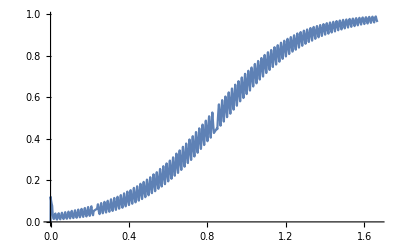

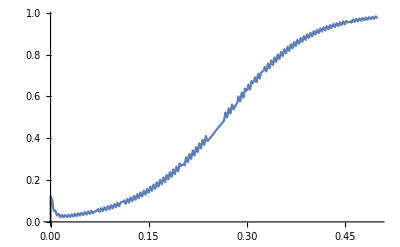

```mathematica
(*Redefine functions using solution*)
fOxSolSlow[t_]:=fOx[t]/. solutionSWVSlow[[1]];
fOxSolFast[t_]:=fOx[t]/. solutionSWVFast[[1]];
VAptamerSolSlow[t_]:=VAptamerGold[t]/. solutionSWVSlow[[1]]
VAptamerSolFast[t_]:=VAptamerGold[t]/. solutionSWVFast[[1]]


iSWVSlow[t_] :=(VSWVSlow[t]-VAptamerGold[t]/. solutionSWVSlow[[1]])/RSol
iSWVFast[t_] :=(VSWVFast[t]-VAptamerGold[t]/. solutionSWVFast[[1]])/RSol;
Plot[{fOxSolSlow[t]},{t,0,Tmax[SquareWaveSlowFreq]}]
Plot[{fOxSolFast[t]},{t,0,Tmax[SquareWaveFastFreq]}]
```

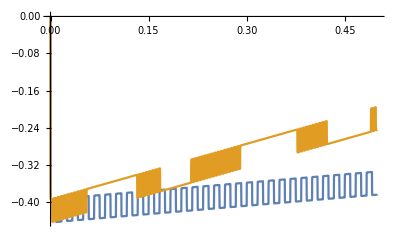

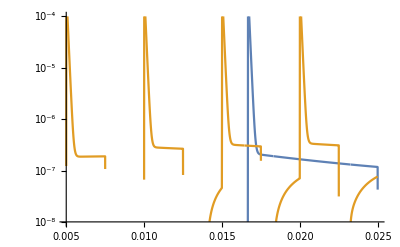

```mathematica
(*Plot total current*)
Plot[{VAptamerSolSlow[t], VAptamerSolFast[t]},{t,0,Tmax[SquareWaveFastFreq]}, PlotRange->{Automatic, Automatic}]
LogPlot[{iSWVSlow[t], iSWVFast[t]},{t,0,Tmax[SquareWaveFastFreq]/20}, PlotRange->{Automatic, {10^-8, 10^-4}}]
```

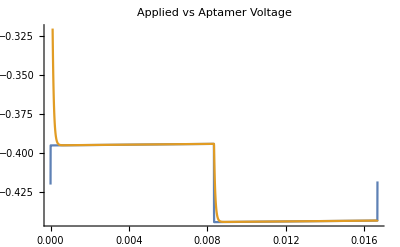

```mathematica
(*Visual Check*)
Plot[{VSWVSlow[t],VAptamerSolSlow[t]},{t,0,Tmax[SquareWaveFastFreq]/30},PlotLabel->"Applied vs Aptamer Voltage"]
```

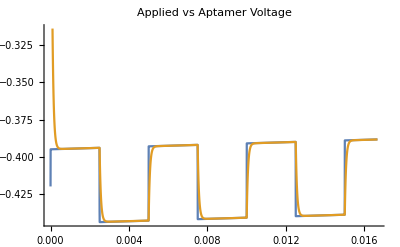

```mathematica
Plot[{VSWVFast[t],VAptamerSolFast[t]},{t,0,Tmax[SquareWaveFastFreq]/30},PlotLabel->"Applied vs Aptamer Voltage"]
```

```mathematica
(*Noise Modeling*)

(*Generate noise values at sampled points*)
(* need to replace this with frequency-domain noise function later! *)
(*Compute Noisy Signal at Sampled Points*)
(*Generate noise values*)
noiseStd=1*10^-12; (*Standard deviation of noise in Amperes*)
noisyCurrentSWVSlow[t_] := iSWVSlow[t] + RandomReal[NormalDistribution[0,noiseStd]];
noisyCurrentSWVFast[t_] := iSWVFast[t] + RandomReal[NormalDistribution[0,noiseStd]];
(*Evaluate model current and add noise*)
```

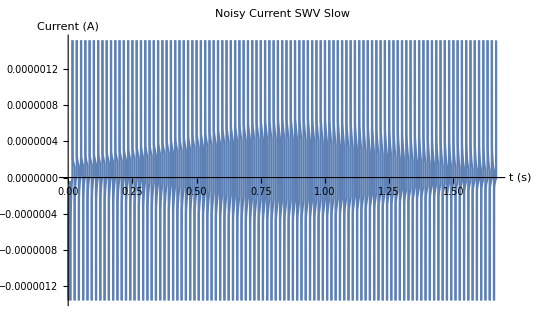

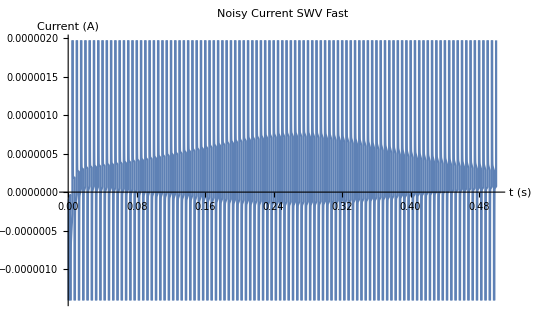

```mathematica
(*Noise Modeling*)(*Generate noise values at sampled points*)noiseStd=1*10^-12; (*Standard deviation of noise in Amperes*)

(*Evaluate timeSamples for specific frequencies*)
tsSlow=timeSamples[SquareWaveSlowFreq];
tsFast=timeSamples[SquareWaveFastFreq];

(*Generate noise vectors once*)
noiseValuesSlow=RandomVariate[NormalDistribution[0,noiseStd],Length[tsSlow]];
noiseValuesFast=RandomVariate[NormalDistribution[0,noiseStd],Length[tsFast]];

(*Compute model current once over timeSamples*)
modelCurrentSWVSlow=Table[iSWVSlow[t],{t,tsSlow}];
modelCurrentSWVFast=Table[iSWVFast[t],{t,tsFast}];

(*Add noise:vectorized*)
noisyCurrentSWVSlowData=Transpose[{tsSlow,modelCurrentSWVSlow+noiseValuesSlow}];
noisyCurrentSWVFastData=Transpose[{tsFast,modelCurrentSWVFast+noiseValuesFast}];

(*Plot to check*)
ListPlot[noisyCurrentSWVSlowData,PlotLabel->"Noisy Current SWV Slow",AxesLabel->{"t (s)","Current (A)"},Joined->True]

ListPlot[noisyCurrentSWVFastData,PlotLabel->"Noisy Current SWV Fast",AxesLabel->{"t (s)","Current (A)"},Joined->True]
```

```mathematica
-Graphics-;
(* from Finding the lost dissociation constant of
electrochemical aptamer-based biosensors *) 


(* maybe we can use above, with an assumption about noise being thermal (proportional to Real R?? *)
(* let's take noise to be a power law function of frequency *)
(* we actually want just an aptamer measured for 12 hours with nothing happenening and then we take the PSD of that *)
(* has anyone measured that ?!?! *)

-Graphics-;
-Graphics-;
(* can we reproduce above? *) 
(* from Comparison of voltammetric methods used in the
interrogation of electrochemical aptamer-based
sensors *)
(*Plot noisy current for Fast SWV over short time*)
```

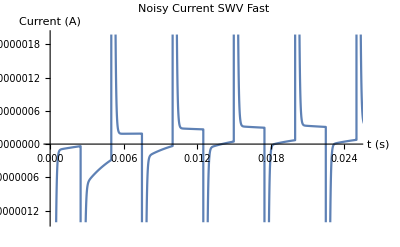

```mathematica
ListPlot[noisyCurrentSWVFastData,PlotLabel->"Noisy Current SWV Fast",AxesLabel->{"t (s)","Current (A)"},PlotRange->{{0,Tmax[SquareWaveFastFreq]/20},Automatic},Joined->True]
```

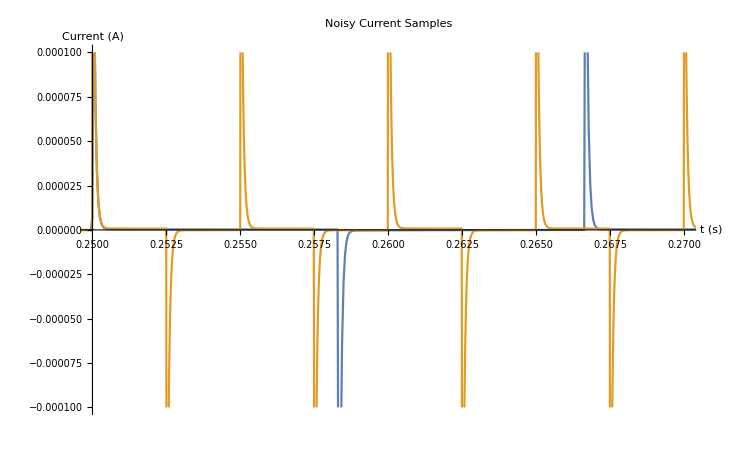

```mathematica
(*Plot both Slow and Fast SWV noisy currents*)
ListPlot[{noisyCurrentSWVSlowData,noisyCurrentSWVFastData},PlotLabel->"Noisy Current Samples",AxesLabel->{"t (s)","Current (A)"},Joined->True,PlotRange->{{Tmax[SquareWaveFastFreq]/2,Tmax[SquareWaveFastFreq]/2+0.02},{-10^-4,1*10^-4}}]
```

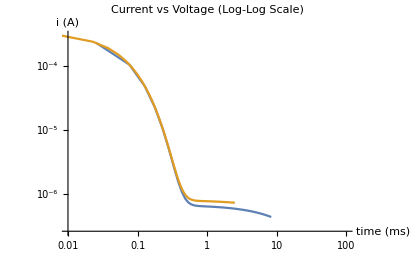

```mathematica
medianUpSwitchTimeSlow=Median[upSwitchTimesSlow];
medianUpSwitchTimeFast=Median[upSwitchTimesFast];


timeRangeSlow=Range[medianUpSwitchTimeSlow,medianUpSwitchTimeSlow+1/(2*SquareWaveSlowFreq),dt[SquareWaveSlowFreq]];
timeRangeFast=Range[medianUpSwitchTimeFast,medianUpSwitchTimeFast+1/(2*SquareWaveFastFreq),dt[SquareWaveFastFreq]];

voltageTimePairsSlow=Select[noisyCurrentSWVSlowData,(Tmax[SquareWaveSlowFreq]/2<=#[[1]]<=Tmax[SquareWaveSlowFreq]/2+1/(2*SquareWaveSlowFreq))&];
voltageTimePairsFast=Select[noisyCurrentSWVFastData,(Tmax[SquareWaveFastFreq]/2<=#[[1]]<=Tmax[SquareWaveFastFreq]/2+1/(2*SquareWaveFastFreq))&];

(*Convert time to ms*)
voltageTimePairsSlow=({(#[[1]]-Tmax[SquareWaveSlowFreq]/2)*1000,#[[2]]}&/@voltageTimePairsSlow);
voltageTimePairsFast=({(#[[1]]-Tmax[SquareWaveFastFreq]/2)*1000,#[[2]]}&/@voltageTimePairsFast);
(*Now plot*)
ListLogLogPlot[{voltageTimePairsSlow,voltageTimePairsFast},AxesLabel->{"time (ms)","i (A)"},PlotLabel->"Current vs Voltage (Log-Log Scale)",PlotRange->{{0.01, 100},Automatic},Joined->True]
```

```mathematica
-Graphics-; (* from Arroyo-Currás et al.2018. Copyright 2018 American Chemical Society *)
```

```mathematica
(* Generate a list of SWV data points *)
(* iForwardSWV and iReverseSWV and IdiffSWV *)
(* First: get the time before each a potential switch in VAptamerGold[t] for forward steps and backward steps *)

(* Next: using the iForwardStepTimes list calculate the current at that time iForwardSWV[t] *) 
(* Next: using the iReverseStepTimes list calculate the current at that time iReverseSWV[t] *) 
(* Finally calculate idiffSWV as the difference between forward and reverse *)
```

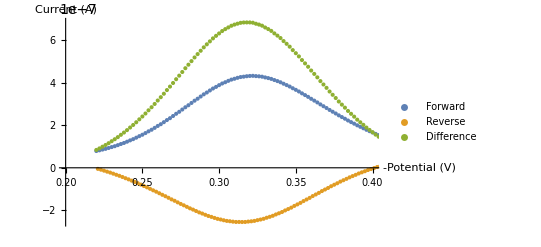

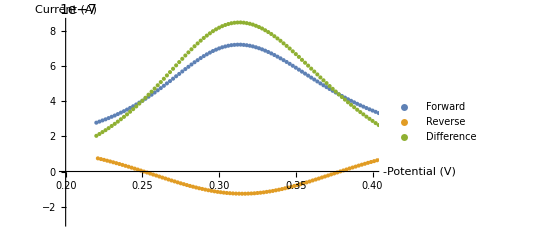

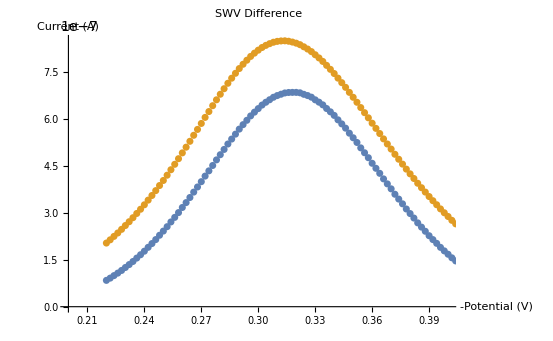

```mathematica
(*Function to find the current value just before each switch time*)(* findPrecedingCurrent[switchTimes_List,data_List]:=Module[{times=data[[All,1]],result},result=Table[Module[{index},index=SelectFirst[Reverse[Range[Length[times]]],times[[#]]<t&,Missing["NotAvailable"]];
If[MissingQ[index],{t,Missing["NotAvailable"]},data[[index]]]],{t,switchTimes}];
result]; *)
findPrecedingCurrent[switchTimes_List,data_List]:=Module[{times=data[[All,1]],result},result=Table[Module[{index},index=SelectFirst[Reverse[Range[3,Length[times]]],(*start from 3 to allow two steps back*)times[[#]]<t&,Missing["NotAvailable"]];
If[MissingQ[index],{t,Missing["NotAvailable"]},data[[index-1]]]],(*go two steps back*){t,switchTimes}];
result];

(*Apply to forward and reverse switches*)
iSWVFWDExpSlow=findPrecedingCurrent[downSwitchTimesSlow,noisyCurrentSWVSlowData];
iSWVREVExpSlow=findPrecedingCurrent[upSwitchTimesSlow,noisyCurrentSWVSlowData];

iSWVFWDExpFast=findPrecedingCurrent[downSwitchTimesFast,noisyCurrentSWVFastData];
iSWVREVExpFast=findPrecedingCurrent[upSwitchTimesFast,noisyCurrentSWVFastData];

(*Calculate difference between forward and reverse steps-Slow*)
iSWVDiffSWVSlow=Table[{-VSWVSlow[upSwitchTimesSlow[[n]]],iSWVFWDExpSlow[[n,2]]-iSWVREVExpSlow[[n,2]]},{n,1,Min[Length[iSWVFWDExpSlow],Length[iSWVREVExpSlow],Length[upSwitchTimesSlow]]}];
iSWVREVvsVSlow=Table[{-VSWVSlow[downSwitchTimesSlow[[n]]],iSWVREVExpSlow[[n,2]]},{n,1,Min[Length[iSWVREVExpSlow],Length[downSwitchTimesSlow]]}];
iSWVFWDvsVSlow=Table[{-VSWVSlow[upSwitchTimesSlow[[n]]],iSWVFWDExpSlow[[n,2]]},{n,1,Min[Length[iSWVFWDExpSlow],Length[upSwitchTimesSlow]]}];

(*Calculate difference between forward and reverse steps-Fast*)
iSWVDiffSWVFast=Table[{-VSWVFast[upSwitchTimesFast[[n]]],iSWVFWDExpFast[[n,2]]-iSWVREVExpFast[[n,2]]},{n,1,Min[Length[iSWVFWDExpFast],Length[iSWVREVExpFast],Length[upSwitchTimesFast]]}];
iSWVREVvsVFast=Table[{-VSWVFast[downSwitchTimesFast[[n]]],iSWVREVExpFast[[n,2]]},{n,1,Min[Length[iSWVREVExpFast],Length[downSwitchTimesFast]]}];
iSWVFWDvsVFast=Table[{-VSWVFast[upSwitchTimesFast[[n]]],iSWVFWDExpFast[[n,2]]},{n,1,Min[Length[iSWVFWDExpFast],Length[upSwitchTimesFast]]}];

(*Plotting*)

ListPlot[{iSWVFWDvsVSlow,iSWVREVvsVSlow,iSWVDiffSWVSlow},AxesLabel->{"-Potential (V)","Current (A)"},PlotRange->{{0.2,0.4},Automatic},PlotLegends->{"Forward","Reverse","Difference"}]
ListPlot[{iSWVFWDvsVFast,iSWVREVvsVFast,iSWVDiffSWVFast},AxesLabel->{"-Potential (V)","Current (A)"},PlotRange->{{0.2,0.4},Automatic},PlotLegends->{"Forward","Reverse","Difference"}]

(*Plot just the difference*)
ListPlot[{iSWVDiffSWVSlow,iSWVDiffSWVFast},AxesLabel->{"-Potential (V)","Current (A)"},PlotRange->{{0.2,0.4},{0,Automatic}},PlotLabel->"SWV Difference"]
```

```mathematica
(* get Square Wave results as a function of period *)
(* Now let's get KDM for 2 representative periods *)
-Graphics-;
```